```mathematica
<< Задача 1.1.2 >>
-Graphics-
Условие: 
-Graphics-
-Graphics-
Решение:
<<1:  Сделаем переход к системе координаи стереографической проекции, геометр. выразив x и y через R и  углы: >>
```

```mathematica
X=(R*Sin[ξ])/(1-Cos[ξ]) Sin[η];
Y=(R*Sin[ξ])/(1-Cos[ξ]) Cos[η];
```

```mathematica
<<2: Для преобразования системы координат находим матрицу Якоби: >>
```

```mathematica
MatrixForm[({{D[X, ξ], D[X, η]}, {D[Y, ξ], D[Y, η]}})]
```

((R Cos[ξ] Sin[η])/(1-Cos[ξ])-(R Sin[η] Sin[ξ]^2)/(1-Cos[ξ])^2 | (R Cos[η] Sin[ξ])/(1-Cos[ξ])
(R Cos[η] Cos[ξ])/(1-Cos[ξ])-(R Cos[η] Sin[ξ]^2)/(1-Cos[ξ])^2 | -(R Sin[η] Sin[ξ])/(1-Cos[ξ]))

```mathematica
<< Теперь найдем транспонированную матрицу Якоби : >>
```

```mathematica
MatrixForm[FullSimplify[Transpose[({{D[X, ξ], D[X, η]}, {D[Y, ξ], D[Y, η]}})]]]
```

((R Sin[η])/(-1+Cos[ξ]) | (R Cos[η])/(-1+Cos[ξ])
R Cos[η] Cot[ξ/2] | -R Cot[ξ/2] Sin[η])

```mathematica
<< 3:Далее, находим Метрический Тензор g
Теперь умножаем матрицу Якоби на транспонированную Матрицу Якоби g=J*J^-T и получаем метрический тензор >>
```

```mathematica
MatrixForm[  FullSimplify[Transpose[({{D[X, ξ], D[X, η]}, {D[Y, ξ], D[Y, η]}})].({{D[X, ξ], D[X, η]}, {D[Y, ξ], D[Y, η]}})]]
```

(1/4 R^2 Csc[ξ/2]^4 | 0
0 | R^2 Cot[ξ/2]^2)

```mathematica
<< Элемент длины dl^2=({{dξ, dη}}).g.*({{dξ}, {dη}}) >>
```

```mathematica
MatrixForm[ FullSimplify[({{dξ, dη}}).({{1/4 R^2 Csc[ξ/2]^4, 0}, {0, R^2 Cot[ξ/2]^2}}).Transpose[({{dξ, dη}})]]]
```

(1/4 R^2 (4 dη^2 Cot[ξ/2]^2+dξ^2 Csc[ξ/2]^4))

```mathematica
<< Далее находим ковариантные скорости ({{Subscript[v, ξ]}, {Subscript[v, η]}})=J^-1*({{Subscript[v, x]}, {Subscript[v, y]}})   >>
```

```mathematica
MatrixForm[  FullSimplify[Inverse[({{D[X, ξ], D[X, η]}, {D[Y, ξ], D[Y, η]}})].({{Subscript[v, x]}, {Subscript[v, y]}})]]
```

(((-1+Cos[ξ]) (Sin[η] v_x+Cos[η] v_y))/R
((Cos[η] v_x-Sin[η] v_y) Tan[ξ/2])/R)

```mathematica
<< При помощи формулы ({{Subscript[v, x]}, {Subscript[v, y]}})= g*({{Subscript[v, ξ]}, {Subscript[v, η]}})  находим контрвариантные скорости от Subscript[v, x] и Subscript[v, y] >>
```

```mathematica
MatrixForm[({{1/4 R^2 Csc[ξ/2]^4, 0}, {0, R^2 Cot[ξ/2]^2}}) .({{((-1+Cos[ξ]) (Sin[η] Subscript[v, x]+Cos[η] Subscript[v, y]))/R}, {((Cos[η] Subscript[v, x]-Sin[η] Subscript[v, y]) Tan[ξ/2])/R}})]
```

(1/4 R (-1+Cos[ξ]) Csc[ξ/2]^4 (Sin[η] v_x+Cos[η] v_y)
R Cot[ξ/2] (Cos[η] v_x-Sin[η] v_y))

```mathematica
<< Положим ξ=ξ[t] и η=η[t],поскольку движение точки зависит от времени >>
```

```mathematica
X[t_]:=(R*Sin[ξ[t]])/(1-Cos[ξ[t]]) Sin[η[t]];
Y[t_]:=(R*Sin[ξ[t]])/(1-Cos[ξ[t]]) Cos[η[t]];
```

```mathematica
<< Найдем матрицу скоростей Subscript[X, t]'=V(x(t)) и Subscript[Y, t]'=V(y(t)) >>
```

```mathematica
MatrixForm[{((R*Sin[ξ[t]])/(1-Cos[ξ[t]]) Sin[η[t]])'[t],((R*Sin[ξ[t]])/(1-Cos[ξ[t]]) Cos[η[t]])'[t]}]
```

(((R Sin[η[t]] Sin[ξ[t]])/(1-Cos[ξ[t]]))'[t]
((R Cos[η[t]] Sin[ξ[t]])/(1-Cos[ξ[t]]))'[t])

```mathematica
<< Запишем в форме матрицы скорости >>
```

```mathematica
∂_t =({{((R Sin[η[t]] Sin[ξ[t]])/(1-Cos[ξ[t]]))'[t]}, {((R Cos[η[t]] Sin[ξ[t]])/(1-Cos[ξ[t]]))'[t]}});
```

```mathematica
<< Находим матрицу ускорений Subscript[X, t]''=V(x(t))'= Subscript[a, x](t) и Subscript[Y, t]''=V(y(t))'=Subscript[a, y](t) >>
```

```mathematica
MatrixForm [[D[{{((R Sin[η[t]] Sin[ξ[t]])/(1-Cos[ξ[t]]))},{((R Cos[η[t]] Sin[ξ[t]])/(1-Cos[ξ[t]]))}}, t,t]]]
```

```mathematica
MatrixForm⟦{{-(R Sin[η[t]] Sin[ξ[t]] η'[t]^2)/(1-Cos[ξ[t]])+(2 R Cos[η[t]] Cos[ξ[t]] η'[t] ξ'[t])/(1-Cos[ξ[t]])-(2 R Cos[η[t]] Sin[ξ[t]]^2 η'[t] ξ'[t])/(1-Cos[ξ[t]])^2-(R Sin[η[t]] Sin[ξ[t]] ξ'[t]^2)/(1-Cos[ξ[t]])-(3 R Cos[ξ[t]] Sin[η[t]] Sin[ξ[t]] ξ'[t]^2)/(1-Cos[ξ[t]])^2+(2 R Sin[η[t]] Sin[ξ[t]]^3 ξ'[t]^2)/(1-Cos[ξ[t]])^3+(R Cos[η[t]] Sin[ξ[t]] η''[t])/(1-Cos[ξ[t]])+(R Cos[ξ[t]] Sin[η[t]] ξ''[t])/(1-Cos[ξ[t]])-(R Sin[η[t]] Sin[ξ[t]]^2 ξ''[t])/(1-Cos[ξ[t]])^2},{-(R Cos[η[t]] Sin[ξ[t]] η'[t]^2)/(1-Cos[ξ[t]])-(2 R Cos[ξ[t]] Sin[η[t]] η'[t] ξ'[t])/(1-Cos[ξ[t]])+(2 R Sin[η[t]] Sin[ξ[t]]^2 η'[t] ξ'[t])/(1-Cos[ξ[t]])^2-(R Cos[η[t]] Sin[ξ[t]] ξ'[t]^2)/(1-Cos[ξ[t]])-(3 R Cos[η[t]] Cos[ξ[t]] Sin[ξ[t]] ξ'[t]^2)/(1-Cos[ξ[t]])^2+(2 R Cos[η[t]] Sin[ξ[t]]^3 ξ'[t]^2)/(1-Cos[ξ[t]])^3-(R Sin[η[t]] Sin[ξ[t]] η''[t])/(1-Cos[ξ[t]])+(R Cos[η[t]] Cos[ξ[t]] ξ''[t])/(1-Cos[ξ[t]])-(R Cos[η[t]] Sin[ξ[t]]^2 ξ''[t])/(1-Cos[ξ[t]])^2}}⟧
```

```mathematica
<< Соотношение между ускорением в декартовой и ковариантным ускорением запишем в форме матрицы ускорения>>
```

```mathematica
MatrixForm[FullSimplify[{{-(R Sin[η[t]] Sin[ξ[t]] η'[t]^2)/(1-Cos[ξ[t]])+(2 R Cos[η[t]] Cos[ξ[t]] η'[t] ξ'[t])/(1-Cos[ξ[t]])-(2 R Cos[η[t]] Sin[ξ[t]]^2 η'[t] ξ'[t])/(1-Cos[ξ[t]])^2-(R Sin[η[t]] Sin[ξ[t]] ξ'[t]^2)/(1-Cos[ξ[t]])-(3 R Cos[ξ[t]] Sin[η[t]] Sin[ξ[t]] ξ'[t]^2)/(1-Cos[ξ[t]])^2+(2 R Sin[η[t]] Sin[ξ[t]]^3 ξ'[t]^2)/(1-Cos[ξ[t]])^3+(R Cos[η[t]] Sin[ξ[t]] η''[t])/(1-Cos[ξ[t]])+(R Cos[ξ[t]] Sin[η[t]] ξ''[t])/(1-Cos[ξ[t]])-(R Sin[η[t]] Sin[ξ[t]]^2 ξ''[t])/(1-Cos[ξ[t]])^2},{-(R Cos[η[t]] Sin[ξ[t]] η'[t]^2)/(1-Cos[ξ[t]])-(2 R Cos[ξ[t]] Sin[η[t]] η'[t] ξ'[t])/(1-Cos[ξ[t]])+(2 R Sin[η[t]] Sin[ξ[t]]^2 η'[t] ξ'[t])/(1-Cos[ξ[t]])^2-(R Cos[η[t]] Sin[ξ[t]] ξ'[t]^2)/(1-Cos[ξ[t]])-(3 R Cos[η[t]] Cos[ξ[t]] Sin[ξ[t]] ξ'[t]^2)/(1-Cos[ξ[t]])^2+(2 R Cos[η[t]] Sin[ξ[t]]^3 ξ'[t]^2)/(1-Cos[ξ[t]])^3-(R Sin[η[t]] Sin[ξ[t]] η''[t])/(1-Cos[ξ[t]])+(R Cos[η[t]] Cos[ξ[t]] ξ''[t])/(1-Cos[ξ[t]])-(R Cos[η[t]] Sin[ξ[t]]^2 ξ''[t])/(1-Cos[ξ[t]])^2}}]]
```

((4 R Sin[ξ[t]/2]^4 (Sin[η[t]] Sin[ξ[t]] η'[t]^2+2 Cos[η[t]] η'[t] ξ'[t]-Cos[η[t]] Sin[ξ[t]] η''[t]+Sin[η[t]] (-Cot[ξ[t]/2] ξ'[t]^2+ξ''[t])))/(-1+Cos[ξ[t]])^3
(4 R Sin[ξ[t]/2]^4 (Cos[η[t]] Sin[ξ[t]] η'[t]^2-2 Sin[η[t]] η'[t] ξ'[t]+Sin[η[t]] Sin[ξ[t]] η''[t]+Cos[η[t]] (-Cot[ξ[t]/2] ξ'[t]^2+ξ''[t])))/(-1+Cos[ξ[t]])^3)

```mathematica
<< Положив радиус равный единице, получаем график x(t) и y(t)(Декартова траекория) >>
```

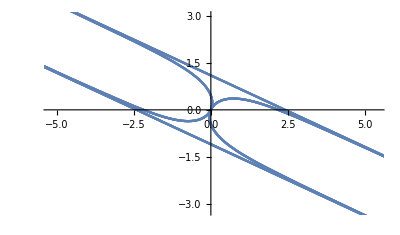

```mathematica
ParametricPlot[{Sin[ξ]/(1-Cos[ξ]) Sin[η],Sin[ξ]/(1-Cos[ξ]) Cos[η]}/.
{η->2-1t,ξ->2t},{t,0,30},, PlotTheme->"Scientific"]
```

```mathematica
X[t_]:=(R*Sin[ξ[t]])/(1-Cos[ξ[t]]) Sin[η[t]];
```

```mathematica
Y[t_]:=(R*Sin[ξ[t]])/(1-Cos[ξ[t]]) Cos[η[t]];
```

```mathematica
η[t_]:=2-1t
```

```mathematica
ξ[t_]:=2t
```

```mathematica
R=1
```

1

```mathematica
<< Рассмотрим график ускорения>>
```

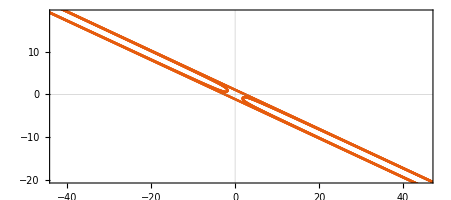

```mathematica
ParametricPlot[Evaluate[{D[D[X[t], t], t],D[D[Y[t], t], t]}],{t,0,30}, PlotTheme->"Scientific"]
```

```mathematica
<< Рассмотрим график скорости>>
```

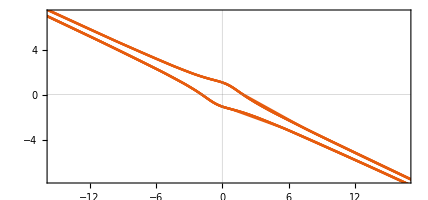

```mathematica
ParametricPlot[Evaluate[{D[X[t],t], D[Y[t],t]}], {t,0,30}, PlotTheme->"Scientific"]
```